```mathematica
(*Patrick T. Tam*)
(*Caída libre*)
```

```mathematica
sol=DSolve[{y'[t]==v[t],v'[t]==-g-(b/m)v[t],y[0]==y0,v[0]==v0},{y[t],v[t]},t]
```

{{v[t]→-(ⅇ^(-(b t)/m) (-g m+ⅇ^((b t)/m) g m-b v0))/b,y[t]→(ⅇ^(-(b t)/m) (-g m^2+ⅇ^((b t)/m) g m^2-b ⅇ^((b t)/m) g m t-b m v0+b ⅇ^((b t)/m) m v0+b^2 ⅇ^((b t)/m) y0))/b^2}}

```mathematica
m=1/10;
g=9.81;
b=1/10;
```

```mathematica
v0=0.;
y0=5.;
```

```mathematica
v[t_]=v[t]/.First@sol
```

-(ⅇ^(-(b t)/m) (-g m+ⅇ^((b t)/m) g m-b v0))/b

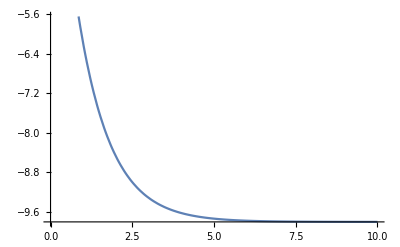

```mathematica
Plot[v[t],{t,0,10}]
```

```mathematica
y[t_]=y[t]/.First@sol
```

100 ⅇ^-t (-0.0981+0.1481 ⅇ^t-0.0981 ⅇ^t t)

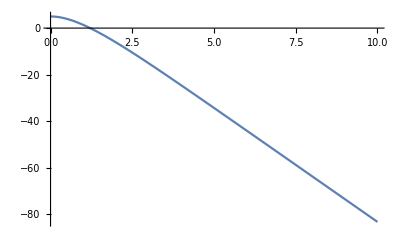

```mathematica
Plot[y[t],{t,0,10}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
v[t_]=v[t]/.First@sol
```

-(ⅇ^(-(b t)/m) (-g m+ⅇ^((b t)/m) g m-b v0))/b

```mathematica
Limit[v[t],t->Infinity]
```

ConditionalExpression[-(g m)/b,(g|v0)∈ℝ&&b m>0]

```mathematica
Manipulate[With[{g=9.81,m=1/10,y0=5.},Plot[{-(g m)/b,-(ⅇ^(-(b t)/m) (-g m+ⅇ^((b t)/m) g m-b v0))/b},{t,0,10},PlotRange->{All,{-20,0}},PlotStyle->{Dashed,Magenta},PlotLabel->"v0 = "<> ToString[(g m)/b]]],{v0,0,3,.1},{b,.01,1,.01}]
```